```mathematica
Clear["Global`*"]
```

## Microbiome care

## Preliminaries

```mathematica
𝓈[u_]:=1-(c+(1-c) u^2)
BB[u1_,u2_,u3_]:=2(u1+u2+u3)-(u1+u2+u3)^2
```

```mathematica
BB[u1_,u2_,u3_]:=1-Exp[-(u1+u2+u3)]
```

```mathematica
m[u_]:=k+(1-k) u^2
```

```mathematica
funsubs={s->𝓈,B->BB,μ->m}
```

{s→𝓈,B→BB,μ→m}

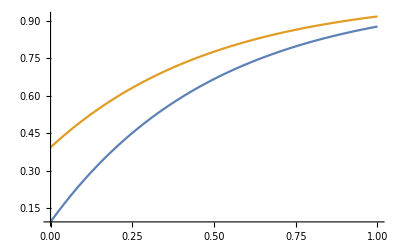

```mathematica
Plot[{BB[u,u,.1],BB[u,u,.5]},{u,0,1}]
```

## Microbiome fitness function

```mathematica
FffMicro=1/2 s[ufocf](((1-d)vf B[uhost1,uhost2,ufocf]μ[uhost1]+d (1-vf)B[uhost1,uhost2,upop]μ[uhost1])/((1-d) s[ulocf]B[uhost1,uhost2,ulocf]+d s[ulocf]B[uhost1,uhost2,upop]))+1/2 s[ufocf]d vf (B[uhost1,uhost2,ufocf]μ[uhost1])/(s[upop]B[uhost1,uhost2,upop])
```

(d vf B[uhost1,uhost2,ufocf] s[ufocf] μ[uhost1])/(2 B[uhost1,uhost2,upop] s[upop])+(s[ufocf] ((1-d) vf B[uhost1,uhost2,ufocf] μ[uhost1]+d (1-vf) B[uhost1,uhost2,upop] μ[uhost1]))/(2 ((1-d) B[uhost1,uhost2,ulocf] s[ulocf]+d B[uhost1,uhost2,upop] s[ulocf]))

```mathematica
FfmMicro=1/2 s[ufocf](((1-d)vf B[uhost1,uhost2,ufocf]μ[uhost2]+d (1-vf)B[uhost1,uhost2,upop]μ[uhost2])/((1-d) s[ulocf]B[uhost1,uhost2,ulocf]+d s[ulocf]B[uhost1,uhost2,upop]))+1/2 s[ufocf]d vf (B[uhost1,uhost2,ufocf]μ[uhost2])/(s[upop]B[uhost1,uhost2,upop])
```

(d vf B[uhost1,uhost2,ufocf] s[ufocf] μ[uhost2])/(2 B[uhost1,uhost2,upop] s[upop])+(s[ufocf] ((1-d) vf B[uhost1,uhost2,ufocf] μ[uhost2]+d (1-vf) B[uhost1,uhost2,upop] μ[uhost2]))/(2 ((1-d) B[uhost1,uhost2,ulocf] s[ulocf]+d B[uhost1,uhost2,upop] s[ulocf]))

```mathematica
FmfMicro=1/2 s[ufocm]/s[ulocm](((1-d)vm B[uhost1,uhost2,ufocm]μ[uhost1]+d(1-vm)B[uhost1,uhost2,upop]μ[uhost1])/((1-d)B[uhost1,uhost2,ulocm]+d B[uhost1,uhost2,upop]))+1/2 s[ufocm]/s[upop] d vm (B[uhost1,uhost2,ufocm]μ[uhost1])/B[uhost1,uhost2,upop]
```

(d vm B[uhost1,uhost2,ufocm] s[ufocm] μ[uhost1])/(2 B[uhost1,uhost2,upop] s[upop])+(s[ufocm] ((1-d) vm B[uhost1,uhost2,ufocm] μ[uhost1]+d (1-vm) B[uhost1,uhost2,upop] μ[uhost1]))/(2 ((1-d) B[uhost1,uhost2,ulocm]+d B[uhost1,uhost2,upop]) s[ulocm])

```mathematica
FmmMicro=1/2 s[ufocm]/s[ulocm](((1-d)vm B[uhost1,uhost2,ufocm]μ[uhost2]+d(1-vm)B[uhost1,uhost2,upop]μ[uhost2])/((1-d)B[uhost1,uhost2,ulocm]+d B[uhost1,uhost2,upop]))+1/2 s[ufocm]/s[upop] d vm (B[uhost1,uhost2,ufocm]μ[uhost2])/B[uhost1,uhost2,upop]
```

(d vm B[uhost1,uhost2,ufocm] s[ufocm] μ[uhost2])/(2 B[uhost1,uhost2,upop] s[upop])+(s[ufocm] ((1-d) vm B[uhost1,uhost2,ufocm] μ[uhost2]+d (1-vm) B[uhost1,uhost2,upop] μ[uhost2]))/(2 ((1-d) B[uhost1,uhost2,ulocm]+d B[uhost1,uhost2,upop]) s[ulocm])

```mathematica
SMicro={{(1-μ[uhost1])vf,(1-μ[uhost1])(1-vm)},{(1-μ[uhost2])(1-vf),(1-μ[uhost2])vm}}
```

{{vf (1-μ[uhost1]),(1-vm) (1-μ[uhost1])},{(1-vf) (1-μ[uhost2]),vm (1-μ[uhost2])}}

```mathematica
FMicro={{FffMicro,FmfMicro},{FfmMicro,FmmMicro}}//FullSimplify
```

{{1/2 s[ufocf] (((-1+d) vf B[uhost1,uhost2,ufocf]+d (-1+vf) B[uhost1,uhost2,upop])/(((-1+d) B[uhost1,uhost2,ulocf]-d B[uhost1,uhost2,upop]) s[ulocf])+(d vf B[uhost1,uhost2,ufocf])/(B[uhost1,uhost2,upop] s[upop])) μ[uhost1],1/2 s[ufocm] (((-1+d) vm B[uhost1,uhost2,ufocm]+d (-1+vm) B[uhost1,uhost2,upop])/(((-1+d) B[uhost1,uhost2,ulocm]-d B[uhost1,uhost2,upop]) s[ulocm])+(d vm B[uhost1,uhost2,ufocm])/(B[uhost1,uhost2,upop] s[upop])) μ[uhost1]},{1/2 s[ufocf] (((-1+d) vf B[uhost1,uhost2,ufocf]+d (-1+vf) B[uhost1,uhost2,upop])/(((-1+d) B[uhost1,uhost2,ulocf]-d B[uhost1,uhost2,upop]) s[ulocf])+(d vf B[uhost1,uhost2,ufocf])/(B[uhost1,uhost2,upop] s[upop])) μ[uhost2],1/2 s[ufocm] (((-1+d) vm B[uhost1,uhost2,ufocm]+d (-1+vm) B[uhost1,uhost2,upop])/(((-1+d) B[uhost1,uhost2,ulocm]-d B[uhost1,uhost2,upop]) s[ulocm])+(d vm B[uhost1,uhost2,ufocm])/(B[uhost1,uhost2,upop] s[upop])) μ[uhost2]}}

### Population dynamics, class frequencies & reproductive values

```mathematica
ℬMicro=1/λ(SMicro+FMicro);
𝒜Micro=ℬMicro/.{ufocf->u,ulocf->u,ufocm->u,ulocm->u,upop->u}//FullSimplify
```

{{(2 vf-(d (-1+vf)+vf) μ[uhost1])/(2 λ),(2-2 vm+(-2+d+3 vm-d vm) μ[uhost1])/(2 λ)},{(2-2 vf+(-2+d+3 vf-d vf) μ[uhost2])/(2 λ),(2 vm-(d (-1+vm)+vm) μ[uhost2])/(2 λ)}}

Position of dominant eigenvalue

```mathematica
evMicrodompos=2
```

2

```mathematica
λ=Eigenvalues[λ 𝒜Micro][[evMicrodompos]]
```

1/4 (2 vf+2 vm+d μ[uhost1]-vf μ[uhost1]-d vf μ[uhost1]+d μ[uhost2]-vm μ[uhost2]-d vm μ[uhost2]+√((-2 vf-2 vm-d μ[uhost1]+vf μ[uhost1]+d vf μ[uhost1]-d μ[uhost2]+vm μ[uhost2]+d vm μ[uhost2])^2-4 (-4+4 vf+4 vm+4 μ[uhost1]-2 d μ[uhost1]-4 vf μ[uhost1]+2 d vf μ[uhost1]-6 vm μ[uhost1]+4 d vm μ[uhost1]+4 vf vm μ[uhost1]-4 d vf vm μ[uhost1]+4 μ[uhost2]-2 d μ[uhost2]-6 vf μ[uhost2]+4 d vf μ[uhost2]-4 vm μ[uhost2]+2 d vm μ[uhost2]+4 vf vm μ[uhost2]-4 d vf vm μ[uhost2]-4 μ[uhost1] μ[uhost2]+4 d μ[uhost1] μ[uhost2]+6 vf μ[uhost1] μ[uhost2]-6 d vf μ[uhost1] μ[uhost2]+6 vm μ[uhost1] μ[uhost2]-6 d vm μ[uhost1] μ[uhost2]-8 vf vm μ[uhost1] μ[uhost2]+8 d vf vm μ[uhost1] μ[uhost2])))

```mathematica
uMicro=Eigenvectors[𝒜Micro][[evMicrodompos]]/Total[Eigenvectors[𝒜Micro][[evMicrodompos]]]//Simplify
```

{(2 vf-2 vm+d μ[uhost1]-vf μ[uhost1]-d vf μ[uhost1]-d μ[uhost2]+vm μ[uhost2]+d vm μ[uhost2]+√(4 (-2+vf+vm)^2+(d (-1+vf)+vf)^2 μ[uhost1]^2+4 (vf (6-5 vm)-(-2+vm)^2+d (-2+3 vf-vm) (-1+vm)) μ[uhost2]+(d (-1+vm)+vm)^2 μ[uhost2]^2+2 μ[uhost1] (-2 (4-4 vf+vf^2+d (-1+vf) (2+vf-3 vm)-6 vm+5 vf vm)+(8-12 vf+d^2 (-1+vf) (-1+vm)-12 vm+17 vf vm+d (-8+11 vf+11 vm-14 vf vm)) μ[uhost2])))/(4-2 vf-2 vm+d μ[uhost1]-vf μ[uhost1]-d vf μ[uhost1]-4 μ[uhost2]+d μ[uhost2]+6 vf μ[uhost2]-2 d vf μ[uhost2]+vm μ[uhost2]+d vm μ[uhost2]+√(4 (-2+vf+vm)^2+(d (-1+vf)+vf)^2 μ[uhost1]^2+4 (vf (6-5 vm)-(-2+vm)^2+d (-2+3 vf-vm) (-1+vm)) μ[uhost2]+(d (-1+vm)+vm)^2 μ[uhost2]^2+2 μ[uhost1] (-2 (4-4 vf+vf^2+d (-1+vf) (2+vf-3 vm)-6 vm+5 vf vm)+(8-12 vf+d^2 (-1+vf) (-1+vm)-12 vm+17 vf vm+d (-8+11 vf+11 vm-14 vf vm)) μ[uhost2]))),-((4 (-1+vf)+2 (2+d (-1+vf)-3 vf) μ[uhost2])/(4-2 vf-2 vm+d μ[uhost1]-vf μ[uhost1]-d vf μ[uhost1]-4 μ[uhost2]+d μ[uhost2]+6 vf μ[uhost2]-2 d vf μ[uhost2]+vm μ[uhost2]+d vm μ[uhost2]+√(4 (-2+vf+vm)^2+(d (-1+vf)+vf)^2 μ[uhost1]^2+4 (vf (6-5 vm)-(-2+vm)^2+d (-2+3 vf-vm) (-1+vm)) μ[uhost2]+(d (-1+vm)+vm)^2 μ[uhost2]^2+2 μ[uhost1] (-2 (4-4 vf+vf^2+d (-1+vf) (2+vf-3 vm)-6 vm+5 vf vm)+(8-12 vf+d^2 (-1+vf) (-1+vm)-12 vm+17 vf vm+d (-8+11 vf+11 vm-14 vf vm)) μ[uhost2]))))}

```mathematica
cMicro=Eigenvectors[Transpose[𝒜Micro]][[evMicrodompos]]/Total[Eigenvectors[Transpose[𝒜Micro]][[evMicrodompos]]]//Simplify;
```

```mathematica
vMicro={cMicro[[1]]/uMicro[[1]],cMicro[[2]]/uMicro[[2]]}//Simplify;
```

```mathematica
uvlistMicro={𝓋[1]->vMicro[[1]],𝓋[2]->vMicro[[2]],𝓊[1]->uMicro[[1]],𝓊[2]->uMicro[[2]]}//Simplify;
```

### Selection gradients on uhost1

```mathematica
Δu=Sum[𝓋[i]𝓊[j](D[ℬMicro[[i,j]],ufocf]+RffMicro D[ℬMicro[[i,j]],ulocf]+D[ℬMicro[[i,j]],ufocm]+RmmMicro D[ℬMicro[[i,j]],ulocm]),{i,1,2},{j,1,2}]/.{ufocf->u,ulocf->u,ufocm->u,ulocm->u,upop->u}//Simplify;
```

## Relatedness coefficients microbe

Relatedness of microbes randomly sampled across two focal adult breeders

```mathematica
Qfmtplus1=(1-μ[uhost1])(1-μ[uhost2])Qfm+(1-μ[uhost1])μ[uhost2](vf/2)+μ[uhost1]μ[uhost2]((vf/2)^2+(vm/2)^2)
```

Qfm (1-μ[uhost1]) (1-μ[uhost2])+1/2 vf (1-μ[uhost1]) μ[uhost2]+(vf^2/4+vm^2/4) μ[uhost1] μ[uhost2]

```mathematica
Qsol=Solve[Qfmtplus1==Qfm,Qfm]//Simplify//Flatten
```

{Qfm→-((2 vf+(-2 vf+vf^2+vm^2) μ[uhost1]) μ[uhost2])/(4 μ[uhost1] (-1+μ[uhost2])-4 μ[uhost2])}

```mathematica
Q/.Qsol
```

Q

Relatedness between a pathogen in a locally born juvenile and a pathon in an adult female

```mathematica
Rlocf=Rlocm=1/2+1/2 Qfm/.Qsol//Simplify
```

1/2-((2 vf+(-2 vf+vf^2+vm^2) μ[uhost1]) μ[uhost2])/(8 μ[uhost1] (-1+μ[uhost2])-8 μ[uhost2])

```mathematica
1/2-((2 vf+(-2 vf+vf^2+vm^2) μ[uhost1]) μ[uhost2])/(8 μ[host1] (-1+μ[host2])-8 μ[host2])
```

1/2-((2 vf+(-2 vf+vf^2+vm^2) μ[uhost1]) μ[uhost2])/(8 μ[host1] (-1+μ[host2])-8 μ[host2])

```mathematica
Rlocf/.{vf->0,vm->0}
```

1/2

## Solution for well-mixed populations

```mathematica
selgradMicroWM=Δu/.uvlistMicro/.{d->1}//Simplify//Flatten
```

(4 (-(-1+vm) μ[uhost2]+μ[uhost1] (1-vf+(-1+vf+vm) μ[uhost2])) (-4 B[uhost1,uhost2,u] s'[u]+4 RmmMicro B[uhost1,uhost2,u] s'[u]+2 vf B[uhost1,uhost2,u] s'[u]+2 RffMicro vf B[uhost1,uhost2,u] s'[u]-4 RmmMicro vf B[uhost1,uhost2,u] s'[u]-2 RffMicro vf^2 B[uhost1,uhost2,u] s'[u]+2 vm B[uhost1,uhost2,u] s'[u]-2 RffMicro vm B[uhost1,uhost2,u] s'[u]-4 RmmMicro vm B[uhost1,uhost2,u] s'[u]+2 RffMicro vf vm B[uhost1,uhost2,u] s'[u]+4 RmmMicro vf vm B[uhost1,uhost2,u] s'[u]-B[uhost1,uhost2,u] μ[uhost1] s'[u]+RffMicro B[uhost1,uhost2,u] μ[uhost1] s'[u]+2 vf B[uhost1,uhost2,u] μ[uhost1] s'[u]-3 RffMicro vf B[uhost1,uhost2,u] μ[uhost1] s'[u]+2 RffMicro vf^2 B[uhost1,uhost2,u] μ[uhost1] s'[u]+3 B[uhost1,uhost2,u] μ[uhost2] s'[u]-RffMicro B[uhost1,uhost2,u] μ[uhost2] s'[u]-2 RmmMicro B[uhost1,uhost2,u] μ[uhost2] s'[u]-4 vf B[uhost1,uhost2,u] μ[uhost2] s'[u]+RffMicro vf B[uhost1,uhost2,u] μ[uhost2] s'[u]+4 RmmMicro vf B[uhost1,uhost2,u] μ[uhost2] s'[u]-2 vm B[uhost1,uhost2,u] μ[uhost2] s'[u]+2 RffMicro vm B[uhost1,uhost2,u] μ[uhost2] s'[u]+2 RmmMicro vm B[uhost1,uhost2,u] μ[uhost2] s'[u]-2 RffMicro vf vm B[uhost1,uhost2,u] μ[uhost2] s'[u]-4 RmmMicro vf vm B[uhost1,uhost2,u] μ[uhost2] s'[u]-B[uhost1,uhost2,u] √(8 (-1+vf+vm) (-2+μ[uhost1]+μ[uhost2])+(2 vf+2 vm+μ[uhost1]-2 vf μ[uhost1]+μ[uhost2]-2 vm μ[uhost2])^2) s'[u]+RffMicro B[uhost1,uhost2,u] √(8 (-1+vf+vm) (-2+μ[uhost1]+μ[uhost2])+(2 vf+2 vm+μ[uhost1]-2 vf μ[uhost1]+μ[uhost2]-2 vm μ[uhost2])^2) s'[u]-RffMicro vf B[uhost1,uhost2,u] √(8 (-1+vf+vm) (-2+μ[uhost1]+μ[uhost2])+(2 vf+2 vm+μ[uhost1]-2 vf μ[uhost1]+μ[uhost2]-2 vm μ[uhost2])^2) s'[u]-2 vf^2 s[u] B^(0,0,1)[uhost1,uhost2,u]-4 vm s[u] B^(0,0,1)[uhost1,uhost2,u]+6 vf vm s[u] B^(0,0,1)[uhost1,uhost2,u]-vf s[u] μ[uhost1] B^(0,0,1)[uhost1,uhost2,u]+2 vf^2 s[u] μ[uhost1] B^(0,0,1)[uhost1,uhost2,u]+vf s[u] μ[uhost2] B^(0,0,1)[uhost1,uhost2,u]+2 vm s[u] μ[uhost2] B^(0,0,1)[uhost1,uhost2,u]-6 vf vm s[u] μ[uhost2] B^(0,0,1)[uhost1,uhost2,u]-vf s[u] √(8 (-1+vf+vm) (-2+μ[uhost1]+μ[uhost2])+(2 vf+2 vm+μ[uhost1]-2 vf μ[uhost1]+μ[uhost2]-2 vm μ[uhost2])^2) B^(0,0,1)[uhost1,uhost2,u]))/(B[uhost1,uhost2,u] s[u] (2-2 vf+(-1+2 vf) μ[uhost2]) (-4-2 vf+6 vm+μ[uhost1]+2 vf μ[uhost1]-4 vm μ[uhost1]+μ[uhost2]-2 vm μ[uhost2]-√(8 (-1+vf+vm) (-2+μ[uhost1]+μ[uhost2])+(2 vf+2 vm+μ[uhost1]-2 vf μ[uhost1]+μ[uhost2]-2 vm μ[uhost2])^2)) (2 vf+2 vm+μ[uhost1]-2 vf μ[uhost1]+μ[uhost2]-2 vm μ[uhost2]+√(8 (-1+vf+vm) (-2+μ[uhost1]+μ[uhost2])+(2 vf+2 vm+μ[uhost1]-2 vf μ[uhost1]+μ[uhost2]-2 vm μ[uhost2])^2)))

```mathematica
selgradMicroWMR/.funsubs//CForm
```

(4*(-((k + (1 - k)*Power(uhost2,2))*(-1 + vm)) + 
       (k + (1 - k)*Power(uhost1,2))*
        (1 - vf + (k + (1 - k)*Power(uhost2,2))*(-1 + vf + vm)))*
     (8*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u + 
       2*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost1,2)) - 
       6*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost2,2)) - 
       4*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*vf - 
       4*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost1,2))*
        vf - Power(E,-u - uhost1 - uhost2)*(1 - c - (1 - c)*Power(u,2))*
        (k + (1 - k)*Power(uhost1,2))*vf + 
       8*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost2,2))*
        vf + Power(E,-u - uhost1 - uhost2)*(1 - c - (1 - c)*Power(u,2))*
        (k + (1 - k)*Power(uhost2,2))*vf - 
       2*Power(E,-u - uhost1 - uhost2)*(1 - c - (1 - c)*Power(u,2))*Power(vf,2) + 
       2*Power(E,-u - uhost1 - uhost2)*(1 - c - (1 - c)*Power(u,2))*
        (k + (1 - k)*Power(uhost1,2))*Power(vf,2) - 
       4*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*vm - 
       4*Power(E,-u - uhost1 - uhost2)*(1 - c - (1 - c)*Power(u,2))*vm + 
       4*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost2,2))*
        vm + 2*Power(E,-u - uhost1 - uhost2)*(1 - c - (1 - c)*Power(u,2))*
        (k + (1 - k)*Power(uhost2,2))*vm + 
       6*Power(E,-u - uhost1 - uhost2)*(1 - c - (1 - c)*Power(u,2))*vf*vm - 
       6*Power(E,-u - uhost1 - uhost2)*(1 - c - (1 - c)*Power(u,2))*
        (k + (1 - k)*Power(uhost2,2))*vf*vm + 
       2*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*
        Sqrt(8*(-2 + 2*k + (1 - k)*Power(uhost1,2) + (1 - k)*Power(uhost2,2))*
           (-1 + vf + vm) + Power(2*k + (1 - k)*Power(uhost1,2) + 
            (1 - k)*Power(uhost2,2) + 2*vf - 2*(k + (1 - k)*Power(uhost1,2))*vf + 
            2*vm - 2*(k + (1 - k)*Power(uhost2,2))*vm,2)) - 
       Power(E,-u - uhost1 - uhost2)*(1 - c - (1 - c)*Power(u,2))*vf*
        Sqrt(8*(-2 + 2*k + (1 - k)*Power(uhost1,2) + (1 - k)*Power(uhost2,2))*
           (-1 + vf + vm) + Power(2*k + (1 - k)*Power(uhost1,2) + 
            (1 - k)*Power(uhost2,2) + 2*vf - 2*(k + (1 - k)*Power(uhost1,2))*vf + 
            2*vm - 2*(k + (1 - k)*Power(uhost2,2))*vm,2)) - 
       8*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*
        (0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) - 
       2*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost1,2))*
        (0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) + 
       6*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost2,2))*
        (0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) + 
       4*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*vf*
        (0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) + 
       6*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost1,2))*
        vf*(0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) - 
       10*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost2,2))*
        vf*(0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) + 
       4*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*Power(vf,2)*
        (0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) - 
       4*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost1,2))*
        Power(vf,2)*(0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) + 
       12*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*vm*
        (0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) - 
       8*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost2,2))*
        vm*(0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) - 
       12*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*vf*vm*
        (0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) + 
       12*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*(k + (1 - k)*Power(uhost2,2))*
        vf*vm*(0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) - 
       2*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*
        Sqrt(8*(-2 + 2*k + (1 - k)*Power(uhost1,2) + (1 - k)*Power(uhost2,2))*
           (-1 + vf + vm) + Power(2*k + (1 - k)*Power(uhost1,2) + 
            (1 - k)*Power(uhost2,2) + 2*vf - 2*(k + (1 - k)*Power(uhost1,2))*vf + 
            2*vm - 2*(k + (1 - k)*Power(uhost2,2))*vm,2))*
        (0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2)))) + 
       2*(1 - c)*(1 - Power(E,-u - uhost1 - uhost2))*u*vf*
        Sqrt(8*(-2 + 2*k + (1 - k)*Power(uhost1,2) + (1 - k)*Power(uhost2,2))*
           (-1 + vf + vm) + Power(2*k + (1 - k)*Power(uhost1,2) + 
            (1 - k)*Power(uhost2,2) + 2*vf - 2*(k + (1 - k)*Power(uhost1,2))*vf + 
            2*vm - 2*(k + (1 - k)*Power(uhost2,2))*vm,2))*
        (0.5 - ((k + (1 - k)*Power(uhost2,2))*
             (2*vf + (k + (1 - k)*Power(uhost1,2))*(-2*vf + Power(vf,2) + Power(vm,2)))
             )/(8*(k + (1 - k)*Power(uhost1,2))*(-1 + k + (1 - k)*Power(uhost2,2)) - 
             8*(k + (1 - k)*Power(uhost2,2))))))/
   ((1 - Power(E,-u - uhost1 - uhost2))*(1 - c - (1 - c)*Power(u,2))*
     (2 - 2*vf + (k + (1 - k)*Power(uhost2,2))*(-1 + 2*vf))*
     (-4 + 2*k + (1 - k)*Power(uhost1,2) + (1 - k)*Power(uhost2,2) - 2*vf + 
       2*(k + (1 - k)*Power(uhost1,2))*vf + 6*vm - 
       4*(k + (1 - k)*Power(uhost1,2))*vm - 2*(k + (1 - k)*Power(uhost2,2))*vm - 
       Sqrt(8*(-2 + 2*k + (1 - k)*Power(uhost1,2) + (1 - k)*Power(uhost2,2))*
          (-1 + vf + vm) + Power(2*k + (1 - k)*Power(uhost1,2) + 
           (1 - k)*Power(uhost2,2) + 2*vf - 2*(k + (1 - k)*Power(uhost1,2))*vf + 
           2*vm - 2*(k + (1 - k)*Power(uhost2,2))*vm,2)))*
     (2*k + (1 - k)*Power(uhost1,2) + (1 - k)*Power(uhost2,2) + 2*vf - 
       2*(k + (1 - k)*Power(uhost1,2))*vf + 2*vm - 
       2*(k + (1 - k)*Power(uhost2,2))*vm + 
       Sqrt(8*(-2 + 2*k + (1 - k)*Power(uhost1,2) + (1 - k)*Power(uhost2,2))*
          (-1 + vf + vm) + Power(2*k + (1 - k)*Power(uhost1,2) + 
           (1 - k)*Power(uhost2,2) + 2*vf - 2*(k + (1 - k)*Power(uhost1,2))*vf + 
           2*vm - 2*(k + (1 - k)*Power(uhost2,2))*vm,2))))

```mathematica
selgradMicroWMR=selgradMicroWM/. {RmmMicro->Rlocf,RffMicro->Rlocm};
```

```mathematica
solvfvm=Table[{vm,u/.FindRoot[selgradMicroWMR/.{vf->vm,s->𝓈,B->BB,μ->m}/.{uhost1->0.25,uhost2->0.25,c->0.8,k->0.8},{u,0.25}]},{vm,0.0,1,0.01}]
```

{{0.,-5.04871×10^-29},{0.01,0.0147168},{0.02,0.0282012},{0.03,0.0406507},{0.04,0.052216},{0.05,0.0630152},{0.06,0.073143},{0.07,0.0826765},{0.08,0.0916798},{0.09,0.100206},{0.1,0.108302},{0.11,0.116006},{0.12,0.123352},{0.13,0.130369},{0.14,0.137083},{0.15,0.143518},{0.16,0.149693},{0.17,0.155626},{0.18,0.161334},{0.19,0.166831},{0.2,0.17213},{0.21,0.177243},{0.22,0.182182},{0.23,0.186955},{0.24,0.191572},{0.25,0.196042},{0.26,0.200371},{0.27,0.204567},{0.28,0.208636},{0.29,0.212584},{0.3,0.216417},{0.31,0.22014},{0.32,0.223758},{0.33,0.227275},{0.34,0.230695},{0.35,0.234022},{0.36,0.23726},{0.37,0.240412},{0.38,0.243482},{0.39,0.246472},{0.4,0.249385},{0.41,0.252223},{0.42,0.25499},{0.43,0.257688},{0.44,0.260318},{0.45,0.262884},{0.46,0.265386},{0.47,0.267827},{0.48,0.270209},{0.49,0.272533},{0.5,0.2748},{0.51,0.277013},{0.52,0.279173},{0.53,0.281281},{0.54,0.283339},{0.55,0.285348},{0.56,0.287308},{0.57,0.289221},{0.58,0.291089},{0.59,0.292912},{0.6,0.294691},{0.61,0.296427},{0.62,0.298121},{0.63,0.299774},{0.64,0.301387},{0.65,0.302961},{0.66,0.304496},{0.67,0.305993},{0.68,0.307452},{0.69,0.308876},{0.7,0.310263},{0.71,0.311616},{0.72,0.312933},{0.73,0.314217},{0.74,0.315468},{0.75,0.316685},{0.76,0.31787},{0.77,0.319024},{0.78,0.320146},{0.79,0.321238},{0.8,0.322299},{0.81,0.32333},{0.82,0.324332},{0.83,0.325306},{0.84,0.32625},{0.85,0.327167},{0.86,0.328055},{0.87,0.328917},{0.88,0.329752},{0.89,0.33056},{0.9,0.331342},{0.91,0.332098},{0.92,0.332829},{0.93,0.333534},{0.94,0.334215},{0.95,0.334872},{0.96,0.335504},{0.97,0.336112},{0.98,0.336698},{0.99,0.337259},{1.,0.337798}}

```mathematica
solvfvm10=Table[{vf,u/.FindRoot[selgradMicroWMR/.{vm->1/10 vf,s->𝓈,B->BB,μ->m}/.{uhost1->0.25,uhost2->0.25,c->0.8,k->0.8},{u,0.25}]},{vf,0.0,1,0.01}]
```

{{0.,-5.04871×10^-29},{0.01,0.0082731},{0.02,0.016164},{0.03,0.0237096},{0.04,0.0309416},{0.05,0.0378867},{0.06,0.0445686},{0.07,0.0510076},{0.08,0.0572216},{0.09,0.0632267},{0.1,0.069037},{0.11,0.0746651},{0.12,0.0801224},{0.13,0.0854192},{0.14,0.0905649},{0.15,0.0955678},{0.16,0.100436},{0.17,0.105176},{0.18,0.109795},{0.19,0.114298},{0.2,0.118691},{0.21,0.12298},{0.22,0.127169},{0.23,0.131262},{0.24,0.135263},{0.25,0.139177},{0.26,0.143006},{0.27,0.146754},{0.28,0.150425},{0.29,0.154021},{0.3,0.157545},{0.31,0.160999},{0.32,0.164387},{0.33,0.167709},{0.34,0.170969},{0.35,0.174168},{0.36,0.177309},{0.37,0.180393},{0.38,0.183422},{0.39,0.186397},{0.4,0.18932},{0.41,0.192193},{0.42,0.195017},{0.43,0.197794},{0.44,0.200524},{0.45,0.203209},{0.46,0.205849},{0.47,0.208447},{0.48,0.211003},{0.49,0.213519},{0.5,0.215994},{0.51,0.21843},{0.52,0.220829},{0.53,0.22319},{0.54,0.225514},{0.55,0.227803},{0.56,0.230057},{0.57,0.232277},{0.58,0.234463},{0.59,0.236617},{0.6,0.238738},{0.61,0.240827},{0.62,0.242886},{0.63,0.244914},{0.64,0.246911},{0.65,0.24888},{0.66,0.250819},{0.67,0.25273},{0.68,0.254613},{0.69,0.256469},{0.7,0.258297},{0.71,0.260098},{0.72,0.261874},{0.73,0.263623},{0.74,0.265346},{0.75,0.267045},{0.76,0.268718},{0.77,0.270367},{0.78,0.271992},{0.79,0.273593},{0.8,0.27517},{0.81,0.276724},{0.82,0.278255},{0.83,0.279763},{0.84,0.281248},{0.85,0.282712},{0.86,0.284153},{0.87,0.285573},{0.88,0.286971},{0.89,0.288348},{0.9,0.289704},{0.91,0.291039},{0.92,0.292354},{0.93,0.293648},{0.94,0.294922},{0.95,0.296175},{0.96,0.29741},{0.97,0.298624},{0.98,0.299819},{0.99,0.300995},{1.,0.302151}}

## Care increases in microbes with increased vertical transmission

```mathematica
a=ListLinePlot[solvfvm,PlotStyle->Red];
b=ListLinePlot[solvfvm10];
```

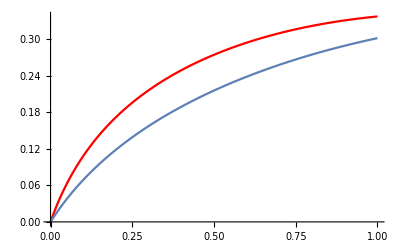

```mathematica
Show[a,b]
```

## Host care

```mathematica
Fff=1/2((1-d) B[uhost1focf,uhost2locfm,upop]μ[uhost1focf])/((1-d)B[uhost1focf,uhost2locfm,upop]+d B[uhost1,uhost2,upop])+1/2 d (B[uhost1focf,uhost2locfm,upop]μ[uhost1])/B[uhost1,uhost2,upop]
```

(d B[uhost1focf,uhost2locfm,upop] μ[uhost1])/(2 B[uhost1,uhost2,upop])+((1-d) B[uhost1focf,uhost2locfm,upop] μ[uhost1focf])/(2 (d B[uhost1,uhost2,upop]+(1-d) B[uhost1focf,uhost2locfm,upop]))

```mathematica
Ffm=1/2((1-d) B[uhost1focf,uhost2locfm,upop]μ[uhost2locfm])/((1-d)B[uhost1focf,uhost2locfm,upop]+d B[uhost1,uhost2,upop])+1/2 d (B[uhost1focf,uhost2locfm,upop]μ[uhost2])/B[uhost1,uhost2,upop]
```

(d B[uhost1focf,uhost2locfm,upop] μ[uhost2])/(2 B[uhost1,uhost2,upop])+((1-d) B[uhost1focf,uhost2locfm,upop] μ[uhost2locfm])/(2 (d B[uhost1,uhost2,upop]+(1-d) B[uhost1focf,uhost2locfm,upop]))

```mathematica
Fmf=1/2((1-d)B[uhost1locmf,uhost2focm,upop]μ[uhost1locmf])/((1-d)B[uhost1locmf,uhost2focm,upop]+d B[uhost1,uhost2,upop])+1/2 d (B[uhost1locmf,uhost2focm,upop]μ[uhost1])/B[uhost1,uhost2,upop]
```

(d B[uhost1locmf,uhost2focm,upop] μ[uhost1])/(2 B[uhost1,uhost2,upop])+((1-d) B[uhost1locmf,uhost2focm,upop] μ[uhost1locmf])/(2 (d B[uhost1,uhost2,upop]+(1-d) B[uhost1locmf,uhost2focm,upop]))

```mathematica
Fmm=1/2((1-d)B[uhost1locmf,uhost2focm,upop]μ[uhost2focm])/((1-d)B[uhost1locmf,uhost2focm,upop]+d B[uhost1,uhost2,upop])+1/2 d (B[uhost1locmf,uhost2focm,upop]μ[uhost2])/B[uhost1,uhost2,upop]
```

(d B[uhost1locmf,uhost2focm,upop] μ[uhost2])/(2 B[uhost1,uhost2,upop])+((1-d) B[uhost1locmf,uhost2focm,upop] μ[uhost2focm])/(2 (d B[uhost1,uhost2,upop]+(1-d) B[uhost1locmf,uhost2focm,upop]))

### Population dynamic

```mathematica
S={{(1-μ[uhost1focf]),0},{0,(1-μ[uhost2focm])}}
```

{{1-μ[uhost1focf],0},{0,1-μ[uhost2focm]}}

```mathematica
F={{Fff,Fmf},{Ffm,Fmm}};
```

```mathematica
ℬ=(S+F);
𝒜=ℬ/.{uhost1focf->uhost1,uhost1locmf->uhost1,uhost2focm->uhost2,uhost2locfm->uhost2}//FullSimplify
```

{{1-μ[uhost1]/2,μ[uhost1]/2},{μ[uhost2]/2,1-μ[uhost2]/2}}

```mathematica
Eigenvalues[𝒜]//Simplify
```

{1,1/2 (2-μ[uhost1]-μ[uhost2])}

```mathematica
uHost=Eigenvectors[𝒜]
```

{{1,1},{-μ[uhost1]/μ[uhost2],1}}

```mathematica
cHost=Eigenvectors[Transpose[𝒜]][[1]]/Total[Eigenvectors[Transpose[𝒜]][[1]]]//Simplify
```

{μ[uhost2]/(μ[uhost1]+μ[uhost2]),μ[uhost1]/(μ[uhost1]+μ[uhost2])}

```mathematica
vHost=cHost 1/2 //Simplify
```

{μ[uhost2]/(2 (μ[uhost1]+μ[uhost2])),μ[uhost1]/(2 (μ[uhost1]+μ[uhost2]))}

```mathematica
uvlist={𝓋[1]->vHost[[1]],𝓋[2]->vHost[[2]],𝓊[1]->1/2,𝓊[2]->1/2}
```

{𝓋[1]→μ[uhost2]/(2 (μ[uhost1]+μ[uhost2])),𝓋[2]→μ[uhost1]/(2 (μ[uhost1]+μ[uhost2])),𝓊[1]→1/2,𝓊[2]→1/2}

### Selection gradients on uhost1, uhost2

```mathematica
Δuhost1=Sum[𝓋[i]𝓊[j]D[ℬ[[i,j]],uhost1focf],{i,1,2},{j,1,2}]/.{uhost1focf->uhost1,uhost1locmf->uhost1,uhost2focm->uhost2,uhost2locfm->uhost2}/.uvlist//Simplify
```

-((μ[uhost2] ((1+d) B[uhost1,uhost2,upop] μ'[uhost1]+2 (-2+d) d μ[uhost1] B^(1,0,0)[uhost1,uhost2,upop]))/(8 B[uhost1,uhost2,upop] (μ[uhost1]+μ[uhost2])))

```mathematica
Δuhost2=Sum[𝓋[i]𝓊[j]D[ℬ[[i,j]],uhost2focm],{i,1,2},{j,1,2}]/.{uhost1focf->uhost1,uhost1locmf->uhost1,uhost2focm->uhost2,uhost2locfm->uhost2}/.uvlist//Simplify
```

-((μ[uhost1] ((1+d) B[uhost1,uhost2,upop] μ'[uhost2]+2 (-2+d) d μ[uhost2] B^(0,1,0)[uhost1,uhost2,upop]))/(8 B[uhost1,uhost2,upop] (μ[uhost1]+μ[uhost2])))

```mathematica
Δuhost1wm=Δuhost1/.{d->1,upop->u}//Simplify
Δuhost2wm=Δuhost2/.{d->1,upop->u}//Simplify
```

(μ[uhost2] (-B[uhost1,uhost2,u] μ'[uhost1]+μ[uhost1] B^(1,0,0)[uhost1,uhost2,u]))/(4 B[uhost1,uhost2,u] (μ[uhost1]+μ[uhost2]))

(μ[uhost1] (-B[uhost1,uhost2,u] μ'[uhost2]+μ[uhost2] B^(0,1,0)[uhost1,uhost2,u]))/(4 B[uhost1,uhost2,u] (μ[uhost1]+μ[uhost2]))

```mathematica
Δuhost2wm/.funsubs//CForm
```

((k + (1 - k)*Power(uhost1,2))*(-2*(1 - Power(E,-u - uhost1 - uhost2))*(1 - k)*
        uhost2 + Power(E,-u - uhost1 - uhost2)*(k + (1 - k)*Power(uhost2,2))))/
   (4.*(1 - Power(E,-u - uhost1 - uhost2))*
     (2*k + (1 - k)*Power(uhost1,2) + (1 - k)*Power(uhost2,2)))

```mathematica
Solve[(Δuhost1==0)/.d->1,μ'[uhost1]]//Simplify
```

{{μ'[uhost1]→(μ[uhost1] B^(1,0,0)[uhost1,uhost2,upop])/B[uhost1,uhost2,upop]}}

```mathematica
Solve[(Δuhost2==0)/.d->1,μ'[uhost2]]//Simplify
```

{{μ'[uhost2]→(μ[uhost2] B^(0,1,0)[uhost1,uhost2,upop])/B[uhost1,uhost2,upop]}}

## Numerical analysis

```mathematica
dwdx[ks_,cs_,vms_,vfs_,{uhost1s_,uhost2s_,us_}]:=
{Δuhost1wm,Δuhost2wm,selgradMicroWMR}/.funsubs/.{k->ks,c->cs,vm->vms,vf->vfs,uhost1->uhost1s,uhost2->uhost2s,u->us}
```

```mathematica
dwdx[0.3,0.8,0.5,0.5,{0.8,0.8,0.3}]
```

{-0.123556,-0.123556,-0.288701}

```mathematica
evolfp[ks_,cs_,vms_,vfs_,init_]:=Module[{sol},
upd[strat_]:=Clip[strat+0.01dwdx[ks,cs,vms,vfs,strat],{0.001,0.999}];
sol=FixedPoint[upd,init,SameTest->(Max[Map[Abs,#1-#2]]<10^-5&)];
Return[sol];
]
```

```mathematica
evolfp[0.3,0.8,0.3,0.3,{0.8,0.7,0.3}]
```

{0.244839,0.236906,0.222097}

```mathematica
evolfp[0.3,0.8,0.003,0.003,{0.8,0.7,0.3}]
```

{0.314517,0.299426,0.00351601}

Numerical results along a range of vertical transmission(equal in both sexes)

```mathematica
outvx=Table[{vx,evolfp[0.3,0.8,vx,vx,{0.8,0.8,0.3}][[1]]},{vx,{0.01,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.99}}]
```

{{0.01,0.306801},{0.05,0.293325},{0.1,0.279149},{0.2,0.25791},{0.3,0.243162},{0.4,0.232541},{0.5,0.224665},{0.6,0.218698},{0.7,0.214104},{0.8,0.210557},{0.9,0.207817},{0.99,0.205895}}

```mathematica
outvxFB=Table[{vx,evolfp[0.3,0.8,vx,0.001vx,{0.8,0.8,0.3}][[1]]},{vx,{0.01,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.99}}]
```

{{0.01,0.308618},{0.05,0.30137},{0.1,0.292815},{0.2,0.277448},{0.3,0.264241},{0.4,0.252908},{0.5,0.243142},{0.6,0.23469},{0.7,0.227329},{0.8,0.220902},{0.9,0.215272},{0.99,0.210797}}

## Main result, vertical transmission indeed reduces duration of care.

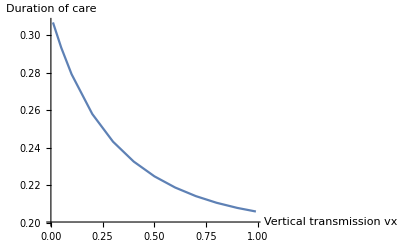

```mathematica
ListLinePlot[outvx,AxesLabel->{"Vertical transmission vx","Duration of care"}]
```

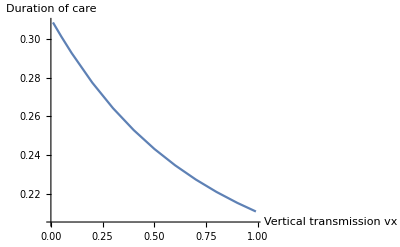

```mathematica
ListLinePlot[outvxFB,AxesLabel->{"Vertical transmission vx","Duration of care"}]
```